# RUNGE-KUTTA

InterpolatingFunction::dmval: Input value {8.01} lies outside the range of data in the interpolating function. Extrapolation will be used.

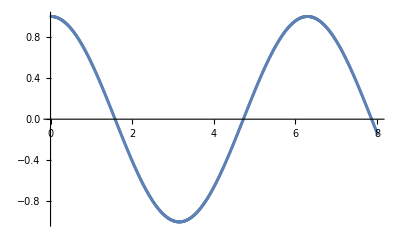

```mathematica
(*TOMA DE DATOS*)
Y[x_]:={y1[x],y2[x]};
f[x_,Y_]:={{0,1},{-1,0}}.Y+{0,10^(-3)*Y[[1]]^3};
Y0={1,0};
x0=0;
xf=8;
h=0.01;


(*SOLUCIÓN EXACTA*)
sol=NDSolve[{y1'[x]==f[x,Y[x]][[1]],y2'[x]==f[x,Y[x]][[2]],y1[x0]==Y0[[1]],y2[x0]==Y0[[2]]},{y1,y2},{x,x0,xf},AccuracyGoal->60,WorkingPrecision->60];


(*MÉTODO*)

liserr={};
Nit=IntegerPart[(xf-x0)/h];
sol1={};
Do[
k1=f[x0,Y0];
k2=f[x0+(1/2)*h,Y0+(1/2)*h*k1];
k3=f[x0+(1/2)*h,Y0+(1/2)*h*k2];
k4=f[x0+h,Y0+h*k3];

Yn=Y0+h(1/6*k1 +1/3*k2 +1/3*k3 + 1/6*k4);
x0=x0+h;
AppendTo[sol1,{x0,Y0[[1]]}];
AppendTo[liserr,{x0,(y1[x0]/.sol)[[1]]-Yn[[1]]}];

Y0=Yn;

,{i,0,Nit}];

ListPlot[sol1]
```

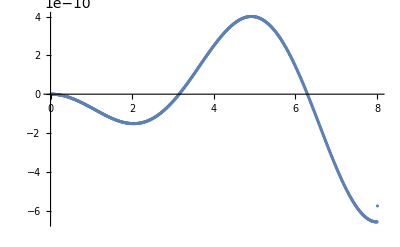

```mathematica
ListPlot[liserr,PlotRange->All]
```